## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TALA2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/home/kevin/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_TALA2_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/home/kevin/Desktop/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | Null
f6p | Null | 0.840336 | 0.798319
0.882353 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | r5p | 0.031 | 0.02945
0.03255 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 135.599 | 128.819
142.379 | 1/s | 8.5 | 37 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 150.792 | 143.252
158.332 | 1/s | 8.5 | 37 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | f6p | 0.0012
Competitive | e4p | 0.00009
Competitive | s7p | 0.000285
Competitive | g3p | 0.000038 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,0,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities={1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | Null
f6p | Null | 0.840336 | 0.798319
0.882353 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 135.599 | 128.819
142.379 | 1/s | 8.5 | 37 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 150.792 | 143.252
158.332 | 1/s | 8.5 | 37 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | f6p | 0.0012
Competitive | e4p | 0.00009
Competitive | s7p | 0.000285
Competitive | g3p | 0.000038 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_TALA2[c] + f6p[c] <=> E_TALA2[c]&f6p",
				"E_TALA2[c]&f6p <=> E_TALA2[c]&mod&g3p",
				"E_TALA2[c]&mod&g3p <=> E_TALA2[c]&mod + g3p[c]",
                                      "E_TALA2[c]&mod + e4p[c] <=> E_TALA2[c]&mod&e4p",
				"E_TALA2[c]&mod&e4p <=> E_TALA2[c]&s7p",
				"E_TALA2[c]&s7p <=> E_TALA2[c] + s7p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c)^TALA22,((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c)^TALA26}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,Overscript[(TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c, TALA22],((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,Overscript[(TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c, TALA26]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

Generating flux equation...

{((TALA2^c&f6p^c)_^-((TALA2^c&mod^c&g3p^c)_^)/K_TALA24) Volume_c k_TALA24^⟶,((TALA2^c&mod^c&e4p^c)_^-((TALA2^c&s7p^c)_^)/K_TALA25) Volume_c k_TALA25^⟶}

Volume_c (-(TALA2^c&mod^c&g3p^c)_^ k_TALA24^⟵+(TALA2^c&f6p^c)_^ k_TALA24^⟶-(TALA2^c&s7p^c)_^ k_TALA25^⟵+(TALA2^c&mod^c&e4p^c)_^ k_TALA25^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{k_TALA2_Kic_pi_1_f6p^⟵/k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟵/k_TALA2_Kic_pi_2_f6p^⟶}

```mathematica
FilePrint@dataPathList
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt"	0.840336135
1	0	0	3.7999999999999996e-6	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	1	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.9090909090909091
1	9.000000000000007e-6	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.86319311139679
1	0.0009000000000000007	1	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.9090909090909093
1	1	0.00011999999999999995	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.09090909090909088
1	1	0.00019018718309533363	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.13680688860321
1	1	0.0003014263717811494	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.20076000891310164
1	1	0.0004777286046641966	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.28474724895080133
1	1	0.0007571488133762321	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.38686317984685703
1	1	0.0011999999999999995	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.49999999999999994
1	1	0.0019018718309533362	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.613136820153143
1	1	0.0030142637178114944	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.7152527510491984
1	1	0.004777286046641966	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.7992399910868982
1	1	0.007571488133762321	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.8631931113967899
1	1	0.011999999999999995	0	0	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.9090909090909092
1	0	0	1	0.0000285	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.09090909090909093
1	0	0	1	0.000045169455985141756	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.13680688860321005
1	0	0	1	0.00007158876329802309	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.2007600089131019
1	0	0	1	0.00011346054360774674	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.28474724895080145
1	0	0	1	0.000179822843176855	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.38686317984685686
1	0	0	1	0.000285	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.5
1	0	0	1	0.00045169455985141755	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.6131368201531432
1	0	0	1	0.000715887632980231	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.7152527510491988
1	0	0	1	0.0011346054360774674	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.7992399910868982
1	0	0	1	0.00179822843176855	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.86319311139679
1	0	0	1	0.00285	0	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.9090909090909091
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	0.002	1	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	135.59891603842877
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.05	0	0	0	1	8.5	37	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt"	150.79207189707626
1	1	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.06249999999999998
1	1	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.1741123948954683
1	1	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.3999999999999999
1	1	0.003794733192202054	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.6782688399674104
1	1	0.011999999999999995	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.8695652173913043
1	1	0.00011999999999999995	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.0476190476190476
1	1	0.00037947331922020535	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.13652705949581428
1	1	0.0011999999999999995	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.33333333333333326
1	1	0.003794733192202054	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.6125741132772069
1	1	0.011999999999999995	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.8333333333333333
1	1	0.00011999999999999995	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.03225806451612902
1	1	0.00037947331922020535	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.09535767393825996
1	1	0.0011999999999999995	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.2499999999999999
1	1	0.003794733192202054	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.513167019494862
1	1	0.011999999999999995	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt"	0.769230769230769
1	9.000000000000007e-6	1	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.06250000000000004
1	0.000028460498941515435	1	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.17411239489546843
1	0.00009000000000000007	1	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.40000000000000013
1	0.00028460498941515434	1	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.6782688399674106
1	0.0009000000000000007	1	0	0	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.8695652173913043
1	9.000000000000007e-6	1	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.04761904761904766
1	0.000028460498941515435	1	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.1365270594958144
1	0.00009000000000000007	1	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.33333333333333354
1	0.00028460498941515434	1	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.612574113277207
1	0.0009000000000000007	1	0	0	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.8333333333333336
1	9.000000000000007e-6	1	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.03225806451612906
1	0.000028460498941515435	1	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.09535767393826003
1	0.00009000000000000007	1	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.25000000000000017
1	0.00028460498941515434	1	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.5131670194948621
1	0.0009000000000000007	1	0	0	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt"	0.7692307692307694
1	0	0	1	0.0000285	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.06250000000000001
1	0	0	1	0.00009012491331479881	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.17411239489546834
1	0	0	1	0.000285	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.39999999999999997
1	0	0	1	0.0009012491331479881	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.6782688399674105
1	0	0	1	0.00285	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.8695652173913043
1	0	0	1	0.0000285	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.04761904761904762
1	0	0	1	0.00009012491331479881	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.13652705949581434
1	0	0	1	0.000285	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.3333333333333333
1	0	0	1	0.0009012491331479881	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.6125741132772069
1	0	0	1	0.00285	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.8333333333333333
1	0	0	1	0.0000285	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.03225806451612904
1	0	0	1	0.00009012491331479881	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.09535767393825997
1	0	0	1	0.000285	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.25
1	0	0	1	0.0009012491331479881	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.513167019494862
1	0	0	1	0.00285	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt"	0.7692307692307693
1	0	0	3.7999999999999996e-6	1	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.062499999999999986
1	0	0	0.000012016655108639841	1	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.17411239489546834
1	0	0	0.000037999999999999995	1	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.3999999999999999
1	0	0	0.0001201665510863984	1	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.6782688399674105
1	0	0	0.00037999999999999997	1	0.0095	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.8695652173913043
1	0	0	3.7999999999999996e-6	1	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.04761904761904761
1	0	0	0.000012016655108639841	1	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.1365270594958143
1	0	0	0.000037999999999999995	1	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.33333333333333326
1	0	0	0.0001201665510863984	1	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.6125741132772068
1	0	0	0.00037999999999999997	1	0.019	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.8333333333333334
1	0	0	3.7999999999999996e-6	1	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.032258064516129024
1	0	0	0.000012016655108639841	1	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.09535767393825997
1	0	0	0.000037999999999999995	1	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.24999999999999997
1	0	0	0.0001201665510863984	1	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.5131670194948619
1	0	0	0.00037999999999999997	1	0.038	1	8.5	30	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt"	0.7692307692307692
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt"	0.019

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	100
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateRev.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateFor.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/absRateRev.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_e4p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateFor_f6p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_g3p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/relRateRev_s7p.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/haldaneRatio_1.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_1.txt, /home/kevin/Desktop/MASSef/examples/fit_TALA2_typeII/input/inhibRatio_pi_2.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.053294515854099
best_fit: 1.0552859403461574
best_fit: 23.34034688013883
best_fit: 23.384972351640823
best_fit: 23.258157764217756
best_fit: 11.667144180466122
best_fit: 1.0865540849807134
best_fit: 11.722398074515565
best_fit: 11.68834191560957
best_fit: 11.681273714982806
best_fit: 0.9870419317918597
best_fit: 11.678835182103551
best_fit: 11.687040354970483
best_fit: 1.0937392742709493
best_fit: 1.0282288126052552
best_fit: 11.68281308825144
best_fit: 11.681829038808873
best_fit: 0.8182073404947734
best_fit: 1.0415299603805614
best_fit: 11.675881088294604
best_fit: 1.06073284272911
best_fit: 0.9947179165019837
best_fit: 11.68802110085157
best_fit: 1.081450501127513
best_fit: 11.666793215584137
best_fit: 11.682227455713951
best_fit: 12.308544131664322
best_fit: 1.08685900879587
best_fit: 1.0545496253047955
best_fit: 11.68177661374462
best_fit: 1.0363923467549423
best_fit: 1.093527491106667
best_fit: 1.092887126417559
best_fit: 11.681624992279204
best_fit: 1.077283553153421
best_fit: 2.594684300645894
best_fit: 1.0865965061079592
best_fit: 11.671003084699594
best_fit: 11.682099650970246
best_fit: 11.683611367064623
best_fit: 23.28192901881276
best_fit: 23.32033050251524
best_fit: 11.657084119986576
best_fit: 0.9737926575476925
best_fit: 23.381061452274917
best_fit: 1.0511532995150985
best_fit: 23.38155624141208
best_fit: 11.681357515994733
best_fit: 0.722923553280667
best_fit: 23.283753231995192
best_fit: 11.681993581424036
best_fit: 11.683277975884947
best_fit: 1.0568399819477972
best_fit: 1.0777419227016627
best_fit: 11.680178590504795
best_fit: 0.9915024272468325
best_fit: 11.681927249173782
best_fit: 11.6583763332144
best_fit: 11.661325944381346
best_fit: 0.9304651200839849
best_fit: 0.9254142531598076
best_fit: 0.8719574066601571
best_fit: 1.0941981017952205
best_fit: 0.9003877639102227
best_fit: 1.0986785049254963
best_fit: 0.7926532504903275
best_fit: 1.0830400479955342
best_fit: 0.9266991170158085
best_fit: 0.9868307249093833
best_fit: 23.422712199873963
best_fit: 1.0939053221671298
best_fit: 11.55730772462944
best_fit: 0.9055162338305432
best_fit: 23.10452163584189
best_fit: 11.682620819093309
best_fit: 1.0899163734286597
best_fit: 23.18914916222266
best_fit: 11.693359900915736
best_fit: 1.0806872941054233
best_fit: 1.0409292489639284
best_fit: 11.65759585687627
best_fit: 1.0269127075545514
best_fit: 1.0198108549905023
best_fit: 10.321959276482618
best_fit: 1.0930230355534545
best_fit: 1.0379073564763153
best_fit: 5.739826289085702
best_fit: 1.0962545201474827
best_fit: 0.7631726635498118
best_fit: 0.9380898599432509
best_fit: 0.9873699969326295
best_fit: 11.60627113264414
best_fit: 23.246048768628228
best_fit: 11.687147315284928
best_fit: 1.097878441016972
best_fit: 0.9509477178794591
best_fit: 1.0190861457063949
best_fit: 1.0120654506979405
best_fit: 1.0991940239574056
best_fit: 1.0996517584285972

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | haldaneRatio_1 | 8.1409×10^-9 | 6.62742×10^-17 | 1.57522×10^-8 | 1.87451×10^-6 | 0.840336 | 0.840336
1 | relRateRev_g3p | 0.000146173 | 2.13666×10^-8 | 0.0000305927 | 0.0336519 | 0.0909091 | 0.0908785
1 | relRateRev_g3p | 0.000137961 | 1.90333×10^-8 | 0.0000434522 | 0.0317617 | 0.136807 | 0.136763
1 | relRateRev_g3p | 0.000126518 | 1.60069×10^-8 | 0.0000584768 | 0.0291277 | 0.20076 | 0.200702
1 | relRateRev_g3p | 0.000111491 | 1.24302×10^-8 | 0.00007309 | 0.0256684 | 0.284747 | 0.284674
1 | relRateRev_g3p | 0.0000932185 | 8.68969×10^-9 | 0.0000830288 | 0.0214621 | 0.386863 | 0.38678
1 | relRateRev_g3p | 0.0000729734 | 5.32512×10^-9 | 0.0000840067 | 0.0168013 | 0.5 | 0.499916
1 | relRateRev_g3p | 0.0000527274 | 2.78017×10^-9 | 0.0000744359 | 0.0121402 | 0.613137 | 0.613062
1 | relRateRev_g3p | 0.0000344527 | 1.18699×10^-9 | 0.000056739 | 0.00793271 | 0.715253 | 0.715196
1 | relRateRev_g3p | 0.0000194218 | 3.77206×10^-10 | 0.0000357415 | 0.00447193 | 0.79924 | 0.799204
1 | relRateRev_g3p | 7.97596×10^-6 | 6.36159×10^-11 | 0.0000158527 | 0.00183652 | 0.863193 | 0.863177
1 | relRateRev_g3p | 2.38655×10^-7 | 5.69563×10^-14 | 4.99567×10^-7 | 0.0000549524 | 0.909091 | 0.909091
1 | relRateFor_e4p | 0.00121427 | 1.47444×10^-6 | 0.000253822 | 0.279205 | 0.0909091 | 0.0906553
1 | relRateFor_e4p | 0.00115107 | 1.32496×10^-6 | 0.000362117 | 0.264692 | 0.136807 | 0.136445
1 | relRateFor_e4p | 0.00106299 | 1.12996×10^-6 | 0.000490786 | 0.244464 | 0.20076 | 0.200269
1 | relRateFor_e4p | 0.000947301 | 8.9738×10^-7 | 0.000620426 | 0.217886 | 0.284747 | 0.284127
1 | relRateFor_e4p | 0.000806595 | 6.50596×10^-7 | 0.000717837 | 0.185553 | 0.386863 | 0.386145
1 | relRateFor_e4p | 0.00065065 | 4.23346×10^-7 | 0.000748528 | 0.149706 | 0.5 | 0.499251
1 | relRateFor_e4p | 0.000494649 | 2.44678×10^-7 | 0.000697948 | 0.113832 | 0.613137 | 0.612439
1 | relRateFor_e4p | 0.000353796 | 1.25172×10^-7 | 0.000582441 | 0.0814315 | 0.715253 | 0.71467
1 | relRateFor_e4p | 0.000237915 | 5.66035×10^-8 | 0.000437719 | 0.0547669 | 0.79924 | 0.798802
1 | relRateFor_e4p | 0.000149655 | 2.23966×10^-8 | 0.000297399 | 0.0344534 | 0.863193 | 0.862896
1 | relRateFor_e4p | 0.0000863015 | 7.44795×10^-9 | 0.000180633 | 0.0198697 | 0.909091 | 0.90891
1 | relRateFor_f6p | 0.000197225 | 3.88975×10^-8 | 0.0000412748 | 0.0454023 | 0.0909091 | 0.0908678
1 | relRateFor_f6p | 0.000160952 | 2.59055×10^-8 | 0.0000506919 | 0.0370536 | 0.136807 | 0.136756
1 | relRateFor_f6p | 0.000110405 | 1.21892×10^-8 | 0.0000510301 | 0.0254184 | 0.20076 | 0.200709
1 | relRateFor_f6p | 0.0000440147 | 1.9373×10^-9 | 0.000028857 | 0.0101343 | 0.284747 | 0.284718
1 | relRateFor_f6p | 0.0000367195 | 1.34832×10^-9 | 0.0000327106 | 0.00845534 | 0.386863 | 0.386896
1 | relRateFor_f6p | 0.000126185 | 1.59225×10^-8 | 0.000145296 | 0.0290593 | 0.5 | 0.500145
1 | relRateFor_f6p | 0.000215668 | 4.65127×10^-8 | 0.000304556 | 0.0496717 | 0.613137 | 0.613441
1 | relRateFor_f6p | 0.000296451 | 8.78829×10^-8 | 0.0004884 | 0.0682836 | 0.715253 | 0.715741
1 | relRateFor_f6p | 0.000362903 | 1.31699×10^-7 | 0.000668136 | 0.0835964 | 0.79924 | 0.799908
1 | relRateFor_f6p | 0.000413511 | 1.70991×10^-7 | 0.000822275 | 0.0952597 | 0.863193 | 0.864015
1 | relRateFor_f6p | 0.000449835 | 2.02351×10^-7 | 0.000942108 | 0.103632 | 0.909091 | 0.910033
1 | relRateRev_s7p | 0.0000848362 | 7.19718×10^-9 | 0.0000177567 | 0.0195323 | 0.0909091 | 0.0908913
1 | relRateRev_s7p | 0.0000743039 | 5.52108×10^-9 | 0.0000234044 | 0.0171077 | 0.136807 | 0.136783
1 | relRateRev_s7p | 0.0000596281 | 3.55551×10^-9 | 0.0000275622 | 0.0137289 | 0.20076 | 0.200732
1 | relRateRev_s7p | 0.0000403541 | 1.62846×10^-9 | 0.0000264572 | 0.00929145 | 0.284747 | 0.284721
1 | relRateRev_s7p | 0.0000169187 | 2.86243×10^-10 | 0.0000150706 | 0.0038956 | 0.386863 | 0.386848
1 | relRateRev_s7p | 9.04747×10^-6 | 8.18566×10^-11 | 0.0000104164 | 0.00208328 | 0.5 | 0.50001
1 | relRateRev_s7p | 0.0000350152 | 1.22606×10^-9 | 0.0000494364 | 0.00806287 | 0.613137 | 0.613186
1 | relRateRev_s7p | 0.0000584547 | 3.41695×10^-9 | 0.0000962773 | 0.0134606 | 0.715253 | 0.715349
1 | relRateRev_s7p | 0.0000777339 | 6.04256×10^-9 | 0.000143068 | 0.0179005 | 0.79924 | 0.799383
1 | relRateRev_s7p | 0.0000924149 | 8.54051×10^-9 | 0.000183701 | 0.0212816 | 0.863193 | 0.863377
1 | relRateRev_s7p | 0.000102951 | 1.0599×10^-8 | 0.00021553 | 0.0237082 | 0.909091 | 0.909306
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183912 | 0.000338236 | 5.86557 | 4.32568 | 135.599 | 141.464
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | absRateFor | 0.0183913 | 0.000338239 | 6.25234 | 4.14633 | 150.792 | 144.54
1 | relRateFor_f6p | 0.0000204723 | 4.19113×10^-10 | 2.94613×10^-6 | 0.0047138 | 0.0625 | 0.0624971
1 | relRateFor_f6p | 0.0000750544 | 5.63317×10^-9 | 0.0000300926 | 0.0172834 | 0.174112 | 0.174142
1 | relRateFor_f6p | 0.000268451 | 7.2066×10^-8 | 0.000247329 | 0.0618323 | 0.4 | 0.400247
1 | relRateFor_f6p | 0.000506813 | 2.5686×10^-7 | 0.000791989 | 0.116766 | 0.678269 | 0.679061
1 | relRateFor_f6p | 0.000670752 | 4.49908×10^-7 | 0.00134405 | 0.154566 | 0.869565 | 0.870909
1 | relRateFor_f6p | 0.000205465 | 4.22158×10^-8 | 0.0000225339 | 0.0473212 | 0.047619 | 0.0476416
1 | relRateFor_f6p | 0.000283599 | 8.04283×10^-8 | 0.0000891827 | 0.0653224 | 0.136527 | 0.136616
1 | relRateFor_f6p | 0.000456606 | 2.08489×10^-7 | 0.000350642 | 0.105193 | 0.333333 | 0.333684
1 | relRateFor_f6p | 0.000702197 | 4.9308×10^-7 | 0.000991252 | 0.161818 | 0.612574 | 0.613565
1 | relRateFor_f6p | 0.000896452 | 8.03625×10^-7 | 0.00172191 | 0.206629 | 0.833333 | 0.835055
1 | relRateFor_f6p | 0.000709335 | 5.03156×10^-7 | 0.0000527303 | 0.163464 | 0.0322581 | 0.0323108
1 | relRateFor_f6p | 0.000764999 | 5.85223×10^-7 | 0.000168118 | 0.176303 | 0.0953577 | 0.0955258
1 | relRateFor_f6p | 0.000901448 | 8.12609×10^-7 | 0.000519454 | 0.207782 | 0.25 | 0.250519
1 | relRateFor_f6p | 0.00113375 | 1.2854×10^-6 | 0.00134141 | 0.261397 | 0.513167 | 0.514508
1 | relRateFor_f6p | 0.00135991 | 1.84935×10^-6 | 0.00241247 | 0.313621 | 0.769231 | 0.771643
1 | relRateFor_e4p | 0.000953077 | 9.08356×10^-7 | 0.000137008 | 0.219213 | 0.0625 | 0.062363
1 | relRateFor_e4p | 0.000832737 | 6.9345×10^-7 | 0.000333531 | 0.191561 | 0.174112 | 0.173779
1 | relRateFor_e4p | 0.000589083 | 3.47019×10^-7 | 0.000542198 | 0.135549 | 0.4 | 0.399458
1 | relRateFor_e4p | 0.00028874 | 8.33709×10^-8 | 0.000450796 | 0.0664628 | 0.678269 | 0.677818
1 | relRateFor_e4p | 0.0000821486 | 6.74838×10^-9 | 0.000164466 | 0.0189136 | 0.869565 | 0.869401
1 | relRateFor_e4p | 0.00068292 | 4.6638×10^-7 | 0.0000748213 | 0.157125 | 0.047619 | 0.0475442
1 | relRateFor_e4p | 0.000611913 | 3.74438×10^-7 | 0.000192229 | 0.140799 | 0.136527 | 0.136335
1 | relRateFor_e4p | 0.000454691 | 2.06744×10^-7 | 0.000348806 | 0.104642 | 0.333333 | 0.332985
1 | relRateFor_e4p | 0.000231517 | 5.36003×10^-8 | 0.000326469 | 0.0532946 | 0.612574 | 0.612248
1 | relRateFor_e4p | 0.0000550017 | 3.02519×10^-9 | 0.000105532 | 0.0126638 | 0.833333 | 0.833228
1 | relRateFor_e4p | 0.000133411 | 1.77985×10^-8 | 9.90784×10^-6 | 0.0307143 | 0.0322581 | 0.0322482
1 | relRateFor_e4p | 0.000117067 | 1.37048×10^-8 | 0.0000257009 | 0.0269521 | 0.0953577 | 0.095332
1 | relRateFor_e4p | 0.0000770106 | 5.93063×10^-9 | 0.0000443269 | 0.0177308 | 0.25 | 0.249956
1 | relRateFor_e4p | 8.8342×10^-6 | 7.8043×10^-11 | 0.0000104385 | 0.00203413 | 0.513167 | 0.513157
1 | relRateFor_e4p | 0.0000575123 | 3.30766×10^-9 | 0.000101874 | 0.0132436 | 0.769231 | 0.769333
1 | relRateRev_s7p | 0.000101652 | 1.03332×10^-8 | 0.0000146272 | 0.0234036 | 0.0625 | 0.0624854
1 | relRateRev_s7p | 0.0000674458 | 4.54893×10^-9 | 0.0000270375 | 0.0155288 | 0.174112 | 0.174085
1 | relRateRev_s7p | 1.79147×10^-6 | 3.20936×10^-12 | 1.65001×10^-6 | 0.000412502 | 0.4 | 0.400002
1 | relRateRev_s7p | 0.0000870994 | 7.5863×10^-9 | 0.000136043 | 0.0200574 | 0.678269 | 0.678405
1 | relRateRev_s7p | 0.000145754 | 2.12443×10^-8 | 0.000291885 | 0.0335668 | 0.869565 | 0.869857
1 | relRateRev_s7p | 0.0000770435 | 5.9357×10^-9 | 8.44683×10^-6 | 0.0177383 | 0.047619 | 0.0476106
1 | relRateRev_s7p | 0.0000467405 | 2.18467×10^-9 | 0.0000146928 | 0.0107618 | 0.136527 | 0.136512
1 | relRateRev_s7p | 0.0000203456 | 4.13942×10^-10 | 0.0000156162 | 0.00468485 | 0.333333 | 0.333349
1 | relRateRev_s7p | 0.000115549 | 1.33516×10^-8 | 0.000163004 | 0.0266097 | 0.612574 | 0.612737
1 | relRateRev_s7p | 0.000190829 | 3.64157×10^-8 | 0.000366247 | 0.0439496 | 0.833333 | 0.8337
1 | relRateRev_s7p | 0.0000162404 | 2.63752×10^-10 | 1.20631×10^-6 | 0.00373957 | 0.0322581 | 0.0322593
1 | relRateRev_s7p | 0.000039394 | 1.55189×10^-9 | 8.65011×10^-6 | 0.00907123 | 0.0953577 | 0.0953663
1 | relRateRev_s7p | 0.0000961433 | 9.24353×10^-9 | 0.0000553507 | 0.0221403 | 0.25 | 0.250055
1 | relRateRev_s7p | 0.000192735 | 3.71468×10^-8 | 0.000227788 | 0.0443887 | 0.513167 | 0.513395
1 | relRateRev_s7p | 0.00028674 | 8.222×10^-8 | 0.000508048 | 0.0660462 | 0.769231 | 0.769739
1 | relRateRev_g3p | 0.0000487843 | 2.37991×10^-9 | 7.02024×10^-6 | 0.0112324 | 0.0625 | 0.062493
1 | relRateRev_g3p | 0.0000400295 | 1.60236×10^-9 | 0.0000160474 | 0.0092167 | 0.174112 | 0.174096
1 | relRateRev_g3p | 0.0000223103 | 4.97751×10^-10 | 0.000020548 | 0.00513701 | 0.4 | 0.399979
1 | relRateRev_g3p | 4.81294×10^-7 | 2.31644×10^-13 | 7.51671×10^-7 | 0.000110822 | 0.678269 | 0.678268
1 | relRateRev_g3p | 0.0000145258 | 2.10997×10^-10 | 0.0000290846 | 0.00334473 | 0.869565 | 0.869594
1 | relRateRev_g3p | 0.0000356398 | 1.27019×10^-9 | 3.90795×10^-6 | 0.00820669 | 0.047619 | 0.047623
1 | relRateRev_g3p | 0.0000353938 | 1.25272×10^-9 | 0.000011127 | 0.00815005 | 0.136527 | 0.136538
1 | relRateRev_g3p | 0.0000348493 | 1.21447×10^-9 | 0.0000267489 | 0.00802467 | 0.333333 | 0.33336
1 | relRateRev_g3p | 0.0000340768 | 1.16123×10^-9 | 0.0000480673 | 0.00784677 | 0.612574 | 0.612622
1 | relRateRev_g3p | 0.000033466 | 1.11997×10^-9 | 0.0000642178 | 0.00770613 | 0.833333 | 0.833398
1 | relRateRev_g3p | 0.000190664 | 3.63528×10^-8 | 0.000014165 | 0.0439116 | 0.0322581 | 0.0322722
1 | relRateRev_g3p | 0.000181458 | 3.29269×10^-8 | 0.0000398508 | 0.0417909 | 0.0953577 | 0.0953975
1 | relRateRev_g3p | 0.000158896 | 2.52479×10^-8 | 0.0000914845 | 0.0365938 | 0.25 | 0.250091
1 | relRateRev_g3p | 0.000120503 | 1.45211×10^-8 | 0.000142408 | 0.0277508 | 0.513167 | 0.513309
1 | relRateRev_g3p | 0.0000831505 | 6.914×10^-9 | 0.000147292 | 0.0191479 | 0.769231 | 0.769378
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_1 | 0.000255834 | 6.54509×10^-8 | 0.0000111892 | 0.0588905 | 0.019 | 0.0189888
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051
1 | inhibRatio_pi_2 | 0.000115708 | 1.33884×10^-8 | 5.06281×10^-6 | 0.0266464 | 0.019 | 0.0190051

### Simulated Data and Best Fit Data Plot

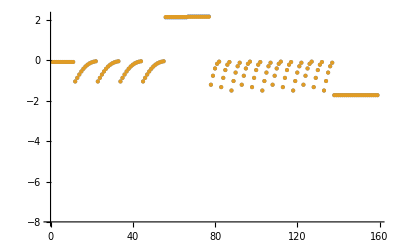

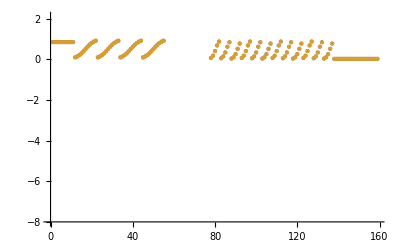

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

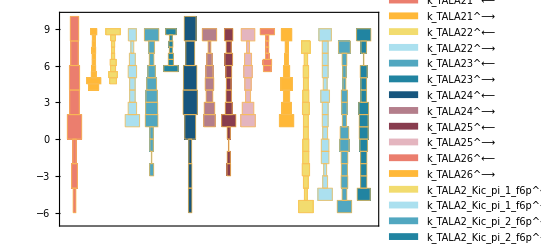

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

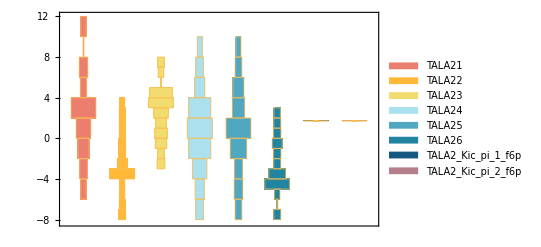

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

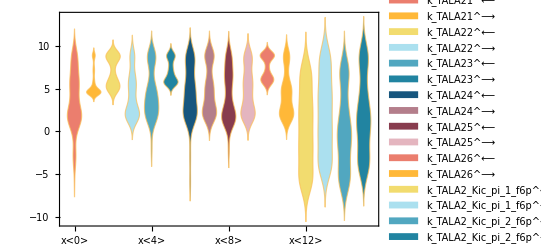

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

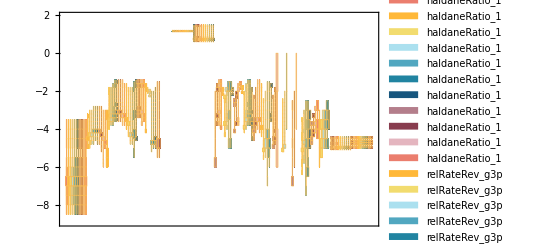

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000038 | 0.0000380128 | 0.033607
0.00009 | 0.0000902698 | 0.299833
0.0012 | 0.0011993 | 0.058032
0.000285 | 0.000284988 | 0.00416528

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
135.599 | 141.464 | 4.32568
150.792 | 144.54 | 4.14633

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.840336 | 1.87451×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.840336 | 1.87451×10^-6

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

Assert::asrtfl: Assertion Length[MASSef`Private`kicList$18447⟦MASSef`Private`inhibI,7⟧⟦All,2⟧]==1 at line 414 in MASSef`analyzeFitResults` failed.

Part::take: Cannot take positions 1 through 5 in {}.

MapThread::mptd: Object {}⟦1;;5⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$18447,MASSef`Private`x$18447][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

Part::take: Cannot take positions 6 through 10 in {}.

General::stop: Further output of Part::take will be suppressed during this calculation.

MapThread::mptd: Object {}⟦6;;10⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$18447,MASSef`Private`x$18447][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

MapThread::mptd: Object {}⟦11;;15⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$18447,MASSef`Private`x$18447][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

data value | predicted value | error in %
0.019 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$18447,MASSef`Private`x$18447],1,1][0]] | 5263.16 Abs[0.019-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$18447,MASSef`Private`x$18447],1,1][0]]]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Assert::asrtfl: Assertion Length[MASSef`Private`kicList$19726⟦MASSef`Private`inhibI,7⟧⟦All,2⟧]==1 at line 414 in MASSef`analyzeFitResults` failed.

Part::take: Cannot take positions 1 through 5 in {}.

MapThread::mptd: Object {}⟦1;;5⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$19726,MASSef`Private`x$19726][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

Part::take: Cannot take positions 6 through 10 in {}.

General::stop: Further output of Part::take will be suppressed during this calculation.

MapThread::mptd: Object {}⟦6;;10⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$19726,MASSef`Private`x$19726][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

MapThread::mptd: Object {}⟦11;;15⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$19726,MASSef`Private`x$19726][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Assert::asrtfl: Assertion Length[MASSef`Private`kicList$20441⟦MASSef`Private`inhibI,7⟧⟦All,2⟧]==1 at line 414 in MASSef`analyzeFitResults` failed.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Assert::asrtfl: Assertion Length[MASSef`Private`kicList$21094⟦MASSef`Private`inhibI,7⟧⟦All,2⟧]==1 at line 414 in MASSef`analyzeFitResults` failed.

General::stop: Further output of Assert::asrtfl will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{Missing[]},{All,All,All}}]; dimensions are 1 and 3.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{Missing[]},{All,All,All}}]; dimensions are 1 and 3.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{Missing[]},{All,All,All}}]; dimensions are 1 and 3.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

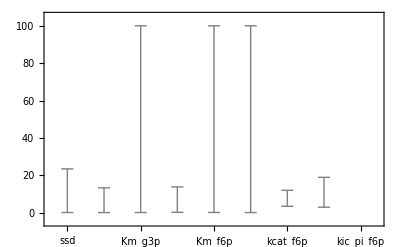

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
{eqnNameList,eqnValList,eqnValListPy,fileList,fileListSub}=exportRateEqs[inputPath,absoluteRateForward,absoluteRateReverse,relativeRateForward,relativeRateReverse,metsSub,metSatForSub,metSatRevSub,rateConstsSub,otherAbsoluteRatesForward,otherAbsoluteRatesReverse];
```